```mathematica
Clear["Global`*"];
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\packages\\2d_toolbox.wl"]
```

```mathematica
MakeRow[bottomcoords_,rodlens_]:=(
c = Length[bottomcoords]-1;
topleftrodid1 = 2*c+2*(c-1) +1;
toprightrodid1 = topleftrodid1+2;
midlevel = Table[ThirdCoord[bottomcoords[[i]],bottomcoords[[i+1]],rodlens[[2*i-1]],rodlens[[2*i]]],{i,1,c}];
topcenter =Table[ThirdCoord[midlevel[[i]],midlevel[[i+1]],rodlens[[2*c+2*i-1]],rodlens[[2*c+2*i]]],{i,1,c-1}];
topleft =ThirdCoord[midlevel[[1]],topcenter[[1]],rodlens[[topleftrodid1]],rodlens[[topleftrodid1+1]]];
topright =ThirdCoord[topcenter[[-1]],midlevel[[-1]],rodlens[[toprightrodid1]],rodlens[[toprightrodid1+1]]];
{bottomcoords,midlevel,topcenter,topleft,topright}
)

LengthToColor[length_]:=If[length>0.98,Darker@Green,Red];

PlotRow[rowcoords_,rodlengths_]:=(
bot = rowcoords[[1]];
mid = rowcoords[[2]];
top = rowcoords[[3]];
left = rowcoords[[4]];
right = rowcoords[[5]];
c = Length[bot]-1;
topleftrodid1 = 2*c+2*(c-1) +1;
toprightrodid1 = topleftrodid1+2;

botposdiag = Table[Style[Line[{bot[[i]],mid[[i]]}],LengthToColor[rodlengths[[2*i-1]]]],{i,1,c}];
botnegdiag = Table[Style[Line[{bot[[i+1]],mid[[i]]}],LengthToColor[rodlengths[[2*i-1+1]]]],{i,1,c}];

topposdiag = Table[Style[Line[{mid[[i]],top[[i]]}],LengthToColor[rodlengths[[2*i-1 + c*2]]]],{i,1,c-1}];
topnegdiag = Table[Style[Line[{mid[[i+1]],top[[i]]}],LengthToColor[rodlengths[[2*i-1+1 + c*2]]]],{i,1,c-1}];

topleft = {Style[Line[{mid[[1]],left}],LengthToColor[rodlengths[[topleftrodid1]]]],
Style[Line[{top[[1]],left}],LengthToColor[rodlengths[[topleftrodid1+1]]]]};
topright = {Style[Line[{mid[[-1]],right}],LengthToColor[rodlengths[[toprightrodid1+1]]]],
Style[Line[{top[[-1]],right}],LengthToColor[rodlengths[[toprightrodid1]]]]};
Join[botposdiag,botnegdiag,topposdiag,topnegdiag, topleft,topright]
)
```

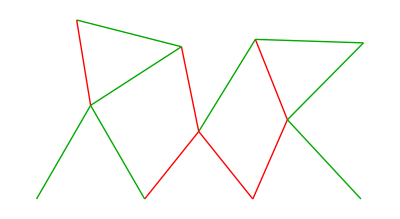

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =1; (*Number fo hourglass rows, r≥1*)
n = (4*c+2)*r ;(*Number of rods*)

rodlengths = RandomChoice[{0.8,1},n];
(*rodlengths = ConstantArray[1,n];*)

fixed = With[{fixedspacing=1},
Table[{x*fixedspacing,0},{x,0,c}]];

rowcoords = MakeRow[fixed,rodlengths];
Graphics[PlotRow[rowcoords,rodlengths]]
```

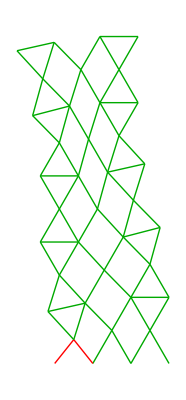

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =5; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)

GetRowTopCoords[makerowoutput_]:=Join[{makerowoutput[[4]]},makerowoutput[[3]],{makerowoutput[[5]]}]

(*rodlengths = RandomChoice[{0.8,1},n];*)
rodlengths = ConstantArray[1,n];
rodlengths[[1]] =short;
rodlengths[[2]] =short;

BuildStructure[c_,r_,rodlengths]:=(
fixed = With[{fixedspacing=1},
Table[{x*fixedspacing,0},{x,0,c}]];

top = fixed;
coordlist = {};
graphicslist={};

Do[rowrodlengths =rodlengths[[i*nr+1;;(i+1)*nr]];
 row = MakeRow[top,rowrodlengths]; 
AppendTo[coordlist,row];
AppendTo[graphicslist,PlotRow[row,rowrodlengths]];
top=GetRowTopCoords[row]
,{i,0,r-1}];
{coordlist,graphicslist})

Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```

```mathematica
|
```

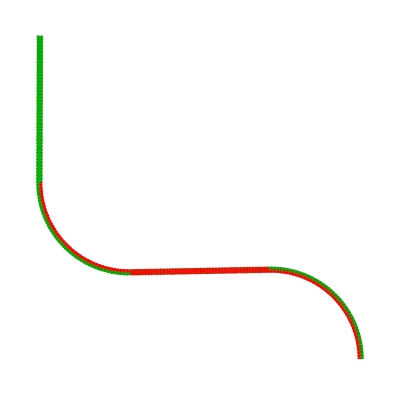

$Aborted

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =90; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)

GetRowTopCoords[makerowoutput_]:=Join[{makerowoutput[[4]]},makerowoutput[[3]],{makerowoutput[[5]]}]

(*rodlengths = RandomChoice[{0.95,1},n];*)

long =1;
short =0.96;
rodlengths = ConstantArray[1,n];

(*leftturn = Join[ConstantArray[short,2*c/3],
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*botrow*)
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*midrow*)
{long,long},
{long,long}]; *)
leftturn = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{short,short},
{long,long}]; (*right hand top tip*)

rightturn = Join[ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{long,long},
{short,short}]; (*right hand top tip*)

short = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{short,long},
{long,short}]; (*right hand top tip*)

long= Join[ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{long,long},
{long,long}]; (*right hand top tip*)

(*rodlengths= Join[leftturn,leftturn];*)
(*rodlengths= Join[rightturn,rightturn];*)
(*rodlengths= Join[short,short];*)

(*rodlengths= Flatten[RandomChoice[{leftturn,rightturn},r]];*)

(*rodlengths= Flatten[ConstantArray[leftturn,r]];*)
rodlengths= Flatten[Join[ConstantArray[leftturn,r/4],ConstantArray[short,r/4],ConstantArray[rightturn,r/4],ConstantArray[long,r/4]]];
(*rodlengths = Join[leftturn,leftturn]*)
(*
rodlengths[[1]]=0.8;
rodlengths[[2]]=0.8;
rodlengths[[3]]=0.8;
rodlengths[[4]]=0.8;

rodlengths[[15]]=0.8;
rodlengths[[9]]=0.8;
(*rodlengths = ConstantArray[1,n];*)
*)

BuildStructure[c_,r_,rodlengths_]:=(
fixed = With[{fixedspacing=1},
Table[{x*fixedspacing,0},{x,0,c}]];

top = fixed;
coordlist = {};
graphicslist={};

Do[rowrodlengths =rodlengths[[i*nr+1;;(i+1)*nr]];
 row = MakeRow[top,rowrodlengths]; 
AppendTo[coordlist,row];
AppendTo[graphicslist,PlotRow[row,rowrodlengths]];
top=GetRowTopCoords[row]
,{i,0,r-1}];
{coordlist,graphicslist})

Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```

```mathematica
RandomChoice[{leftturn,rightturn,short,long},2]
```

{{1,1,1,1,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,1,1,1,1,1,1,1,0.8,0.8,0.8,1,1,0.8,0.8},{1,1,1,1,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,1,1,1,1,1,1,1,0.8,0.8,0.8,1,1,0.8,0.8}}